```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]-s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

LaplaceTransformToSetByState[Q_,start_,hit_List,s_]:=Module[{n=Length[Q],subStates,m,results,eqMatrix,eqRHS,hj,sol,iPos},(*If'start' is already in'hit',then the time is 0 with prob=1=>transform=1,but specifically we don't "hit h_j first" if j!=that state.We'll handle it below.*)If[MemberQ[hit,start],(*Then we trivially return a vector of dimension Length[hit],where the entry for'start' is 1,and all others 0.*)
Return[Map[If[#==start,1,0]&,hit]]];
(*Otherwise,we solve one linear system for each h_j in'hit'.*)
subStates=Complement[Range[n],hit];(*non-absorbing set*)m=Length[subStates];
results=Table[((*Build the (Q-sI) submatrix for non-absorbing states.*)eqMatrix=Table[Q[[subStates[[i]],subStates[[j]]]],{i,m},{j,m}];
Do[eqMatrix[[i,i]]-=s,{i,1,m}];
(*RHS=-Q_{i,h_j},for each i in subStates.*)
eqRHS=Table[-Q[[subStates[[i]],hj]],{i,1,m}];
(*Solve and get phi_i^(j)(s).Then extract the'start' component.*)
sol=LinearSolve[eqMatrix,eqRHS];
iPos=First@Position[subStates,start];
sol[[iPos]]),{hj,hit}  (*for each absorbing state in'hit'*)];
Return[results];];

LogSpecificity[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights,ss,kboff,konb,kuon,kbon,koffu,kuoff},
{kboff,konb,kuon,kbon,koffu,kuoff} = Table[rates[[i]][[1]]/.rates[[i]],{i,1,Length[rates]}];
weights={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb};
Q = RateMatrix[edges, weights,6];
ss = SteadyStateProbabilities[Q];
Log[ss[[3]]/ss[[5]]] + Log[ω/γ]
]
```

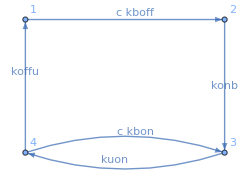

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Pure ligand, 1 binding site ***)

(*Edge lists and weights*)
edges1={{1,2},{2,3},{3,4},{4,3},{4,1}};
weights1={c*kboff,konb,kuon,c*kbon,koffu};
nstates1 = 4;
nedges1 = 5;

(*Plot the circuit*)
edgeList=Table[edges1[[i,1]]->edges1[[i,2]],{i,1,nedges1}];
g=Graph[edges1,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights1)[[i]],0.55],{i,1,nedges1}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{4,1},{3,2}}}]
```

```mathematica
Q1= RateMatrix[edges1, weights1, nstates1];
ss1 = SteadyStateProbabilities[Q1];

(*Mean first passage times*)
meanToff=MeanFirstPassageTimes2[Q1][[1,3]][[1]];
meanTon = MeanFirstPassageTimes2[Q1][[3,1]][[1]];
tau = meanToff + meanTon;

(*Variance of first passage times*)
varToff = FullSimplify[VarianceFirstPassageTimes[Q1][[1,3]]][[1]][[1]];
varTon = FullSimplify[VarianceFirstPassageTimes[Q1][[3,1]]][[1]][[1]];
```

```mathematica
(*Validating the Laplace transform FPT means and variances*)
Foff = LaplaceTransformFPT[Q1,s1][[1,3]][[1]];
Fon = LaplaceTransformFPT[Q1,s2][[3,1]][[1]];
meanToffLt = FullSimplify[-With[{s1=0},Evaluate[D[Foff,{s1,1}]]]];
meanTonLt = FullSimplify[-With[{s2=0},Evaluate[D[Fon,{s2,1}]]]];
varToffLt = FullSimplify[With[{s1=0},Evaluate[D[Foff,{s1,2}]]]-meanToffLt^2];
varTonLt = FullSimplify[With[{s2=0},Evaluate[D[Fon,{s2,2}]]]-meanTonLt^2];

On[Assert];
Assert[meanToffLt==meanToff]
Assert[meanTonLt==meanTon]
Assert[varToffLt==varToff]
Assert[varTonLt==varTon]
```

```mathematica
(*MM estimators*)
cHatOff = c/.Solve[meanToff==sampleToff,c][[1]];
cHatOn = c/.Solve[meanTon==sampleTon,c][[1]];

(*Variances of estimators*)
VarCHatOff = Simplify[With[{sampleToff = meanToff}, Evaluate[D[cHatOff, {sampleToff,1}]^2]]*varToff];
VarCHatOn = Simplify[With[{sampleTon = meanTon}, Evaluate[D[cHatOn, {sampleTon,1}]^2]]*varTon];
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
dotFoff = FullSimplify[c^2 / (tau*VarCHatOff)];
dotFon = FullSimplify[c^2 / (tau*VarCHatOn)];
dotF = dotFoff + dotFon;
```

```mathematica
FullSimplify[dotFoff]
```

(c kboff koffu konb^3 kuon)/((c^2 kboff^2+konb^2) (c kboff (c kbon+koffu) konb+koffu konb kuon+c kboff (koffu+konb) kuon))

```mathematica
(*Maximize Fisher information rate*)
NMaximize[{With[{c=50},Evaluate[dotFoff]],0<kboff<0.0888,0<konb<5,0<kuon<5,0<kbon<0.0888,0<koffu<5 },{kboff,konb,kuon,kbon,koffu}]
```

{0.8,{kboff→0.05,konb→5.,kuon→5.,kbon→-9.9875×10^-9,koffu→5.}}

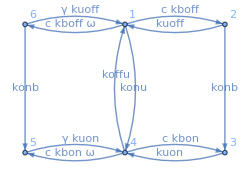

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},{4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
F1off = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = F1off[[3]][[1]]*F31 +F1off[[2]][[1]]*F41 + F1off[[1]][[1]]*F51;
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt];

(*Covariance matrix*)
Subscript[Σ, x] = Simplify[{{varToffLt,covTonToff},{covTonToff,varTonLt}}];
```

```mathematica
(*MM estimators*)
Subscript[ĉ, off] =Simplify[c/.Solve[meanToffLt==sampleToff,c][[1]]];
Subscript[ĉ, on] = FullSimplify[c/.Solve[meanTonLt==sampleTon,c][[1]]];

(*Jacobian*)
Subscript[OverHat[dc], off]  = Simplify[With[{sampleToff = meanToffLt}, Evaluate[D[Subscript[ĉ, off], {sampleToff,1}]]]];
Subscript[OverHat[dc], on]  = Simplify[With[{sampleTon = meanTonLt}, Evaluate[D[Subscript[ĉ, on], {sampleTon,1}]]]];
delf = {{Subscript[OverHat[dc], off],0},{0,Subscript[OverHat[dc], on] }};

(*Covariance matrix of estimators*)
Subscript[Σ, y] = delfᵀ.Subscript[Σ, x].delf;
```

```mathematica
(*Combined estimator and its variance*)
Subscript[σ2, off] = Subscript[Σ, y][[1,1]];
Subscript[σ2, on] = Subscript[Σ, y][[2,2]];
Cov = Subscript[Σ, y][[1,2]];
ρ = Cov/(Subscript[σ2, off]*Subscript[σ2, on]);

ĉ = (Subscript[ĉ, off]*(Subscript[σ2, on]-Cov) + Subscript[ĉ, on]*(Subscript[σ2, off]-Cov))/(Subscript[σ2, off] + Subscript[σ2, on] - 2Cov);
σ2 = (Subscript[σ2, on]*Subscript[σ2, off] - Cov^2)/(Subscript[σ2, off] + Subscript[σ2, on] - 2Cov);
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
Subscript[F, off] = c^2/ (τ*Subscript[σ2, off]);
Subscript[F, on] = c^2/ (τ*Subscript[σ2, on]);
F = c^2/ (τ*σ2);
```

```mathematica
(*Maximize Fisher information rate*)
kmin = 0.00001;
kmax = 5;
kdifflim = 0.0888;
cvals = Table[10.^x, {x,Subdivide[-1.5,2.5,1]}];
wvals = Table[10.^x, {x,Subdivide[-2,2.5,1]}];
results = Table[NMaximize[{With[{c=x, ω=y,γ=10},Evaluate[F]],kmin<kboff<kdifflim,kmin<konb<kmax,kmin<kuon<kmax,kmin<kbon<kdifflim,kmin<koffu<kmax,kmin<kuoff<kmax,kmin<konu<kmax },{kboff,konb,kuon,kbon,koffu,kuoff,konu}],{x, cvals},{y,wvals}];
```

```mathematica
(*Saving data*)
file = FileNameJoin[{$HomeDirectory},".julia/dev/LLROpt/mathematica-nbs/data/20250324/max-F-vs-c-vs-w.wl"]
Save[file, results]
```

/home/tohme/.julia/dev/LLROpt/mathematica-nbs/data/20250324/max-F-vs-c-vs-w.wl

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*** Tests ***)

pathList = {{1,3},{3,1},{1,5},{5,1},{4,5},{5,4}};

(*Mean first passage times*)
M2 = MeanFirstPassageTimes2[Q2];
meanTs = Table[M2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Variance of first passage times*)
V2 = VarianceFirstPassageTimes[Q2];
varTs = Table[V2[[pathList[[i,1]],pathList[[i,2]]]][[1]][[1]],{i,1,6}];
```

```mathematica
(*Laplace*)
F2= LaplaceTransformFPT[Q2,s];
laplaceTs = Table[F2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Check that mean Ton and var Ton from both methods agree*)
dF = Table[With[{s=0}, Evaluate[D[Fij, {s,1}]]],{Fij,laplaceTs}];
d2F = Table[With[{s=0}, Evaluate[D[Fij, {s,2}]]],{Fij,laplaceTs}];
```

```mathematica
varsLt = Table[d2F[[i]] - dF[[i]]^2,{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[-dF[[i]]] == FullSimplify[meanTs[[i]]]],{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[Expand[varsLt[[i]]]] == FullSimplify[Expand[varTs[[i]]]]],{i,1,6}];
```

```mathematica
(*Comparing with built-in functions*)
mproc1 = ContinuousMarkovProcess[1,Q2];
mproc3 = ContinuousMarkovProcess[3,Q2];
mproc5 = ContinuousMarkovProcess[5,Q2];
```

```mathematica
dist13 = FirstPassageTimeDistribution[mproc1,3];
dist15 = FirstPassageTimeDistribution[mproc1,5];
dist31 = FirstPassageTimeDistribution[mproc3,1];
dist51 = FirstPassageTimeDistribution[mproc5,1];
distToff = FirstPassageTimeDistribution[mproc1,{3,5}];
```

```mathematica
meanToffBuiltin = FullSimplify[Mean[distToff]]
```

(1+((konb+kuoff) (konb+kuoff γ))/(c kboff (konb+kuoff γ+(konb+kuoff) ω)))/konb

```mathematica
FullSimplify[meanToffLt]
```

(1+((konb+kuoff) (konb+kuoff γ))/(c kboff (konb+kuoff γ+(konb+kuoff) ω)))/konb

```mathematica
With[{c=1, ω=1,γ=1,kboff=1,konb=1,kuon=1,kbon=0,koffu=1,kuoff=0,s1=0,s2=0},Evaluate[meanToffLt]]
```

3/2

```mathematica
FullSimplify[Variance[pdfT135]]
```

((konb+kuoff)^2 (konb+kuoff γ)^2+c^2 kboff^2 (konb+kuoff γ+(konb+kuoff) ω)^2+2 c kboff kuoff ((konb+kuoff γ)^2+(konb+kuoff)^2 γ ω))/(c^2 kboff^2 konb^2 (konb+kuoff γ+(konb+kuoff) ω)^2)